## 画图

### 需要的基础函数

```mathematica
Clear["Global`*"]
(*需要的函数*)
re[th_]:=170/2/Pi th;
Toxy[th_]:={re[th]Cos[th],re[th]Sin[th]};
x[th_]:=Toxy[th][[1]];
y[th_]:=Toxy[th][[2]];
k[th_]:=-x'[th]/y'[th]
dth[th_]:=ArcTan[y[th]/x[th]]-ArcTan[k[th]];
r1[th_]:=re[th]/3/Abs@Cos[dth[th]];
s=900Pi/170;
```

### 分块绘图

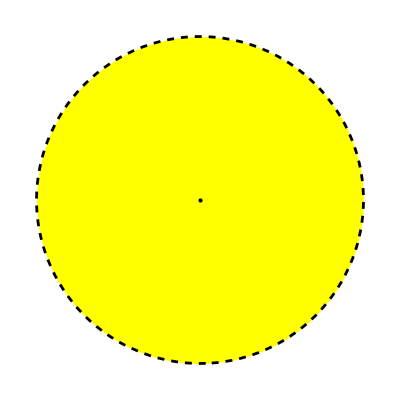

```mathematica
(*分块绘图*)
YelloDisk=Show[
(*底盘*)
Graphics[{{Yellow,Disk[{0,0},450]},Point[{0,0}]}],
ContourPlot[x^2+y^2==450^2,{x,-450,450},{y,-450,450},ContourStyle->{Black,Dashed}]]
```

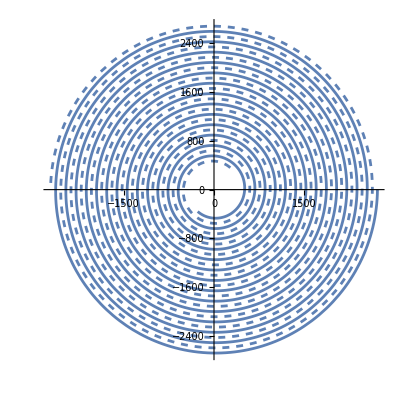

```mathematica
InAndOutSpiral=Show[
(*盘入轨迹,用实线*)
PolarPlot[170/(2Pi)t,{t,s,32Pi},PlotStyle->{Medium}],
(*盘出轨迹,用虚线*)
PolarPlot[-170/(2Pi)t,{t,s,32Pi},PlotStyle->{Dashed,Medium}]
]
```

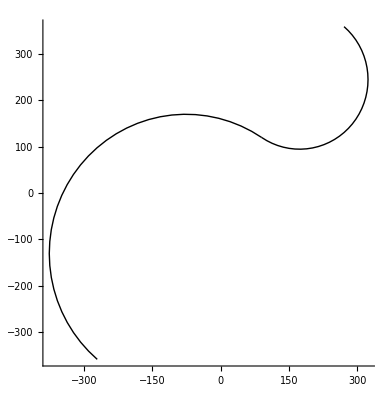

```mathematica
(*圆内的掉头轨迹*)
(*大圆的圆心,起点*)
{bigCircleStart,bigCircleEnd,smallCircleStart,smallCircleEnd}=With[{
positiveDirection=Sign[{1,k[s]}~Dot~Toxy[s]] ,(*圆弧的正确指向方向*)
unit=Normalize[{1,k[s]}](*半径方向的单位向量*)
},
bigCircleCenter=Toxy[s]-positiveDirection 2r1[s]unit;
smallCircleCenter=-(Toxy[s]-positiveDirection r1[s]unit);
ArcTan@@#&/@{
Toxy[s]-bigCircleCenter,
-1/3Toxy[s]-bigCircleCenter,
-Toxy[s]-smallCircleCenter,
-1/3Toxy[s]-smallCircleCenter
}
];
(*大圆图*)
bigCirclePic=Graphics[Circle[bigCircleCenter,2r1[s],{bigCircleEnd-2Pi,bigCircleStart}],Axes->True];
(*小圆图*)
smallCirclePic=Graphics[Circle[smallCircleCenter,r1[s],{smallCircleStart,smallCircleEnd}]];
(*所有内部轨迹*)
insidePath=Show[bigCirclePic,smallCirclePic]
```

```mathematica
(*连结的辅助线/辅助圆点等*)
lines={Black,Line[{Toxy[s],-Toxy[s]}],Red,Line[{Toxy[s],bigCircleCenter,smallCircleCenter,-Toxy[s]}]};
circleCenters=Point[{bigCircleCenter,smallCircleCenter,{0,0}}];
```

### 绘图

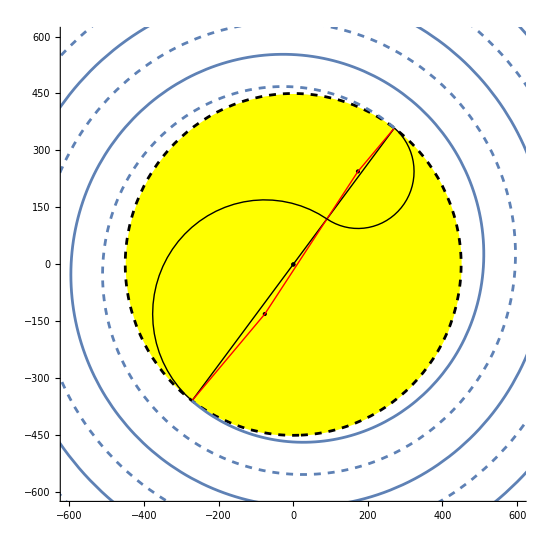

```mathematica
Show[
YelloDisk,Graphics[{circleCenters,lines}],insidePath,InAndOutSpiral,
PlotRange->{{-600,600},{-600,600}},Axes->True
]
```

### 导出二级数据

```mathematica
N[#,10]&@{Toxy[s],2/3(-Toxy[s])+1/3Toxy[s],-Toxy[s]}
```

{{-271.1855864,-359.1077523},{90.39519546,119.7025841},{271.1855864,359.1077523}}

```mathematica
bigCircleCenter//N[#,9]&
2r1[s]//N[#,9]&
```

{-76.0009117,-130.572643}

300.541767

```mathematica
smallCircleCenter//N[#,9]&
r1[s]//N[#,9]&
```

{173.593249,244.840197}

150.270883

```mathematica
2^25
```

33554432

```mathematica
Toxy[s]//N
```

{-271.186,-359.108}

```mathematica
2/1.5869458
```

1.26028